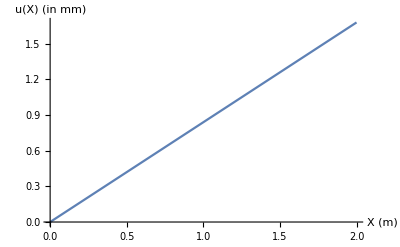

```mathematica
L=2; (*in m*)
α=12 10^-6; (*1/degree centigrade*)
Ε=1.0 10^11; (*in Pa*)
ΔT=80-10; (*in degree centigrade*)
δ=α ΔT L//N;
u[X_]:=α ΔT X
Plot[u[X] 10^3,{X,0,L},AxesLabel->{"X (m)","u(X) (in mm)"}]
```

```mathematica
u[2]//N
```

0.00168

```mathematica
ToExpression["
\\left\\{
\\begin{array}{ll}
\\pi (10~\\rm cm)^4/2, && 0\\le X \\le 120 ~\\rm cm,\\\\
\\pi (6~\\rm cm)^4/2, && 120< X \\le 200 ~\\rm cm,
\\end{array}
\\right.
",TeXForm]
```

ToExpression::esntx: Could not parse 
\left\{
\begin{array}{ll}
\pi (10~\rm cm)^4/2, && 0\…)^4/2, && 120< X \le 200 ~\rm cm,
\end{array}
\right.
 as input.

$Failed

```mathematica
?ToExpression
```

```mathematica
ClearAll[J]
T=10 10^3; (* in Newtons*)
G=26 10^9
J[X_]:=Piecewise[{
{π/2(20/2  10^-2)^4,0≤ X≤1.2},
{π/2(12/2  10^-2)^4 ,2.0≥ X>1.2}
}
]
```

26000000000

```mathematica
Integrate[T/(J[X] G),{X,0,2}]*180/π
```

1.03434

```mathematica
ClearAll[J,T,G]

T[X_]:=Piecewise[{
{2250,0≤ X≤0.6},
{2250 ,0.6< X≤ 0.8},
{250,0.8< X≤ 1.2}
}
]
G=77 10^9
J[X_]:=Piecewise[{
{0.904 10^-6,0≤ X≤0.6},
{1.272 10^-6 ,0.6< X≤ 0.8},
{0.0795 10^-6 ,0.8< X≤ 1.2}
}
]
```

77000000000

```mathematica
Integrate[T[X]/(G J[X]),{X,0,1.2}]
```

0.0403247